```mathematica
Spectrum[g_Graph]:=Sort[Tally@Eigenvalues@AdjacencyMatrix[g],NumericalOrder];
Spectrum[m_]:=Sort[Tally@Eigenvalues[m],NumericalOrder];
SecondEigenvalue[g_Graph]:=RankedMax[Eigenvalues[AdjacencyMatrix[g],3],2];
SecondEigenvalue[m_]:=RankedMax[Eigenvalues[m,3],2]
```

```mathematica
GMatrix[sigma_Integer,k_Integer]:=#+Transpose[#]&[SparseArray[Join[
Flatten[Table[{i(k+1)+u,i(k+1)+v},{i,0,2sigma-2},{u,2sigma-1,k},{v,u+1,k+1}],2],
Flatten[Table[{{i(k+1)+u,i(k+1)+v},{i(k+1)+u+1,i(k+1)+v}},{i,0,2sigma-2},{u,1,2sigma-3,2},{v,u+2,k+1}],3],
Flatten[Table[{i(k+1)+2j,Mod[i+j,2sigma-1](k+1)+2j-1},{i,0,2sigma-2},{j,sigma-1}],1]
]->1,{(2sigma-1)(k+1),(2sigma-1)(k+1)}]];
G[sigma_Integer,k_Integer,opts___]:=AdjacencyGraph[GMatrix[sigma,k],opts]
```

```mathematica
QuotientAdjacencyMatrix[g_Graph,s_List]:=SparseArray@Flatten[If[#1==#2,{#1,#2}->(2#3)/Length[s⟦#1⟧],{{#1,#2}->#3/Length[s⟦#1⟧],{#2,#1}->#3/Length[s⟦#2⟧]}]&@@@({First[#1],Last[#1],#2}&@@@Tally[EdgeList[g]/.Flatten[Thread/@MapIndexed[Rule[#1,First[#2]]&,s],1]]),1]
```

Factor f_(ζ^j)(x) of the characteristic polynomial of quotient matrix for some m and 0 ≤ j ≤ 2m-2.

```mathematica
ClearAll[f];
f[m_,0]:=-(x+1)^(2m-2)(x-k);
f[m_,j_]:=With[{g=GCD[2m-1,j]},(2ChebyshevT[(2m-1)/g,(x+1)/2])^(g-1)((k-2m+1-x)ChebyshevT[(2m-1)/g,(x+1)/2]/((x+1)/2)+(2m-1)(ChebyshevU[(2m-1)/g-1,(x+1)/2]-ChebyshevU[(2m-1)/g-2,(x+1)/2]))]
```

Characteristic polynomial of quotient matrix

```mathematica
ClearAll[p];
p[m_]:=Product[f[m,j],{j,0,2m-2}]//Factor
```

```mathematica
(*f[sigma_]:=f[sigma]={Collect[#1,{x,k}],#2}&@@@FactorList@CharacteristicPolynomial[Normal@QuotientAdjacencyMatrix[G[sigma,2sigma],Join[Table[{i,j},{i,2sigma-1},{j,2sigma-1,2sigma+1}],List/@Flatten[Table[{i,j},{i,2sigma-1},{j,2sigma-2}],1]]]/.{2->k-2sigma+2,3->k-2sigma+3},x]*)
```

### Small Examples

Graph W_4 for σ = 2.

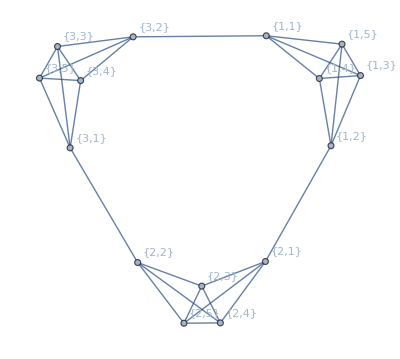

```mathematica
G[2,4,VertexLabels->Automatic]
```

Spectrum and Characteristic Polynomial of Quotient Matrix

```mathematica
Spectrum[%]
```

{{Root-2.20Root[5-7 #1-2 #1^2+#1^3&,1]-2.2044015503294316,2},{-1,8},{Root0.636Root[5-7 #1-2 #1^2+#1^3&,2]0.6355519407979247,2},{Root3.57Root[5-7 #1-2 #1^2+#1^3&,3]3.5688496095315068,2},{4,1}}

```mathematica
f[2]
```

{{1,1},{k-x,1},{1+x,2},{3-2 k+(-1+2 k) x+(-2+k) x^2-x^3,2}}

Vertex Partition and Quotient Matrix of W_4.

```mathematica
Join[Table[{i,j},{i,3},{j,3,5}],List/@Flatten[Table[{i,j},{i,3},{j,2}],1]]
```

{{{1,3},{1,4},{1,5}},{{2,3},{2,4},{2,5}},{{3,3},{3,4},{3,5}},{{1,1}},{{1,2}},{{2,1}},{{2,2}},{{3,1}},{{3,2}}}

```mathematica
Normal@QuotientAdjacencyMatrix[G[2,4],%]/.{2->k-2,3->k-1}//MatrixForm
```

(-2+k | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0
0 | -2+k | 0 | 0 | 0 | 1 | 1 | 0 | 0
0 | 0 | -2+k | 0 | 0 | 0 | 0 | 1 | 1
-1+k | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
-1+k | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | -1+k | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | -1+k | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | -1+k | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | -1+k | 1 | 0 | 0 | 0 | 0 | 0)

Z_10 for σ = 3.

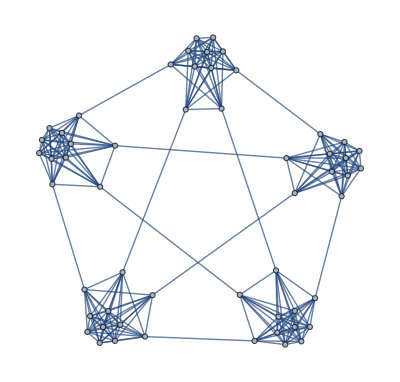

```mathematica
G[3,10]
```

```mathematica
Spectrum[%]
```

{{Root-2.67Root[-5+46 #1-11 #1^2-34 #1^3-6 #1^4+#1^5&,1]-2.673406618914421,4},{Root-1.94Root[-5+46 #1-11 #1^2-34 #1^3-6 #1^4+#1^5&,2]-1.9371580400262038,4},{-1,34},{Root0.113Root[-5+46 #1-11 #1^2-34 #1^3-6 #1^4+#1^5&,3]0.11282166160568745,4},{Root0.891Root[-5+46 #1-11 #1^2-34 #1^3-6 #1^4+#1^5&,4]0.8907593482328576,4},{Root9.61Root[-5+46 #1-11 #1^2-34 #1^3-6 #1^4+#1^5&,5]9.60698364910208,4},{10,1}}

```mathematica
f[3]
```

{{1,1},{k-x,1},{1+x,4},{-5+k+(14-6 k) x+(1+k) x^2+(-6+4 k) x^3+(-4+k) x^4-x^5,4}}

A_8 for σ = 4.

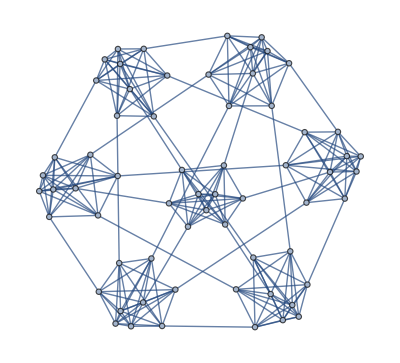

```mathematica
G[4,8]
```

```mathematica
Spectrum[%]
```

{{Root-2.79Root[-8-19 #1+68 #1^2+37 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,1]-2.790292237102982,6},{Root-2.22Root[-8-19 #1+68 #1^2+37 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,2]-2.219894418526786,6},{Root-1.52Root[-8-19 #1+68 #1^2+37 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,3]-1.5230990939427331,6},{-1,20},{Root-0.244Root[-8-19 #1+68 #1^2+37 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,4]-0.24413307321199104,6},{Root0.503Root[-8-19 #1+68 #1^2+37 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,5]0.502880455004431,6},{Root0.942Root[-8-19 #1+68 #1^2+37 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,6]0.9419581784639768,6},{Root7.33Root[-8-19 #1+68 #1^2+37 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,7]7.332580189316085,6},{8,1}}

```mathematica
f[4]
```

{{1,1},{k-x,1},{1+x,6},{k+(-29+6 k) x+(36-13 k) x^2+(27-8 k) x^3+(-13+8 k) x^4+(-15+6 k) x^5+(-6+k) x^6-x^7,6}}

```mathematica
With[{v=First[v[5,10]]},Flatten@Outer[TwoWayRule,v[1],v[-1]]]
```

{5<->1,5<->12,5<->23,5<->34,5<->45,5<->56,5<->67,5<->78,5<->89,16<->1,16<->12,16<->23,16<->34,16<->45,16<->56,16<->67,16<->78,16<->89,31<->1,31<->12,31<->23,31<->34,31<->45,31<->56,31<->67,31<->78,31<->89,38<->1,38<->12,38<->23,38<->34,38<->45,38<->56,38<->67,38<->78,38<->89,49<->1,49<->12,49<->23,49<->34,49<->45,49<->56,49<->67,49<->78,49<->89,64<->1,64<->12,64<->23,64<->34,64<->45,64<->56,64<->67,64<->78,64<->89,71<->1,71<->12,71<->23,71<->34,71<->45,71<->56,71<->67,71<->78,71<->89,82<->1,82<->12,82<->23,82<->34,82<->45,82<->56,82<->67,82<->78,82<->89,99<->1,99<->12,99<->23,99<->34,99<->45,99<->56,99<->67,99<->78,99<->89}

```mathematica
ClearAll[f];
f[m_,k_,v_]:=HighlightGraph[G[m,k],{v[1],Style[v[-1],Green],Style[Flatten@Table[i(k+1)+j,{i,2m-1},{j,2m-1,k+1}],EdgeForm[{Thick,Blue}]],Style[Flatten@Outer[TwoWayRule,v[1],v[-1]],Purple,Thick]}]
```

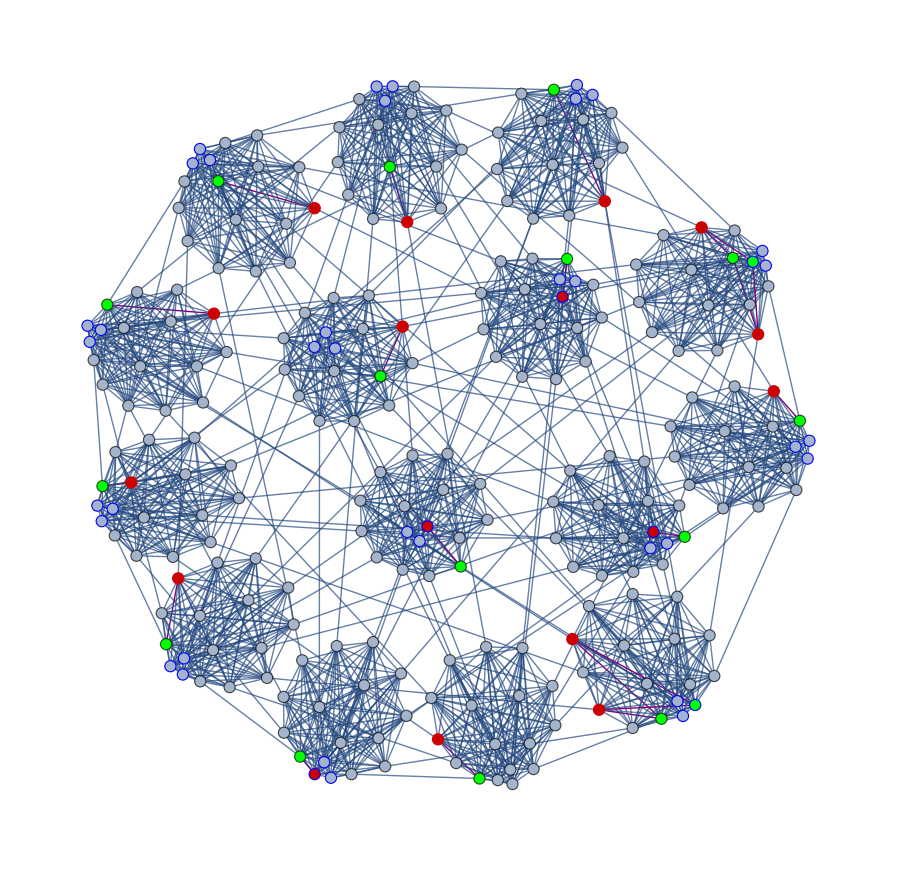

```mathematica
f[8,16,First@v[8,16]]
```

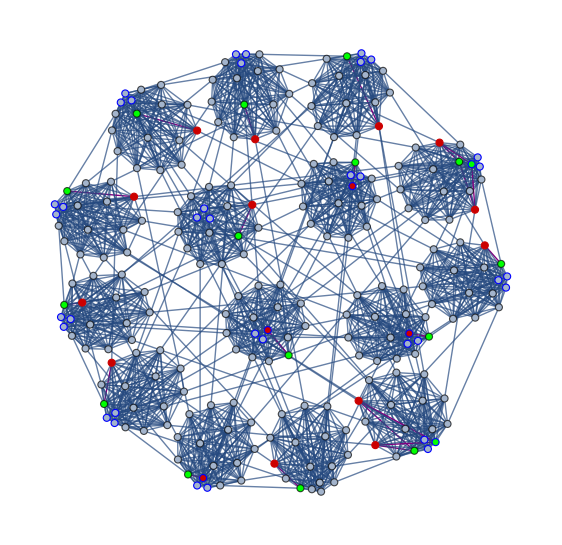

```mathematica
f[8,16,v[8,16]⟦3⟧]
```

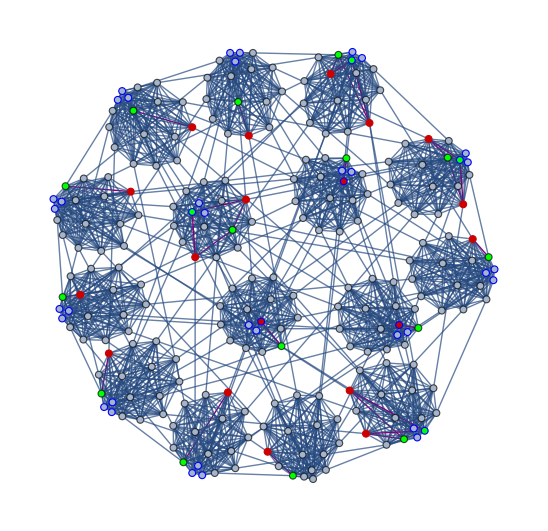

```mathematica
f[8,16,v[8,16]⟦8⟧]
```

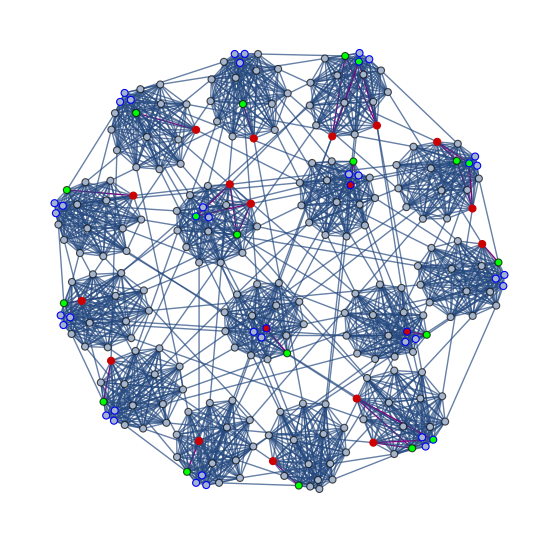

```mathematica
f[8,16,v[8,16]⟦9⟧]
```

Eigenvalues and eigenvectors of G_(m,k) for -1.

```mathematica
e[m_,k_]:=e[m,k]=(2m-1)(k+1)-MatrixRank[GMatrix[m,k]+IdentityMatrix[(2m-1)(k+1)]]
```

```mathematica
v[m_,k_]:=KeyDrop[PositionIndex[#],0]&/@NullSpace[GMatrix[m,k]+IdentityMatrix[(2m-1)(k+1)]]
```

```mathematica
Table[e[m,k],{m,2,12},{k,2m,2m+5}]//TableForm
```

8 | 11 | 14 | 17 | 20 | 23
14 | 19 | 24 | 29 | 34 | 39
20 | 27 | 34 | 41 | 48 | 55
30 | 39 | 48 | 57 | 66 | 75
32 | 43 | 54 | 65 | 76 | 87
38 | 51 | 64 | 77 | 90 | 103
60 | 75 | 90 | 105 | 120 | 135
50 | 67 | 84 | 101 | 118 | 135
56 | 75 | 94 | 113 | 132 | 151
86 | 107 | 128 | 149 | 170 | 191
68 | 91 | 114 | 137 | 160 | 183

```mathematica
Table[e[m,k]-((2m-1)(k-2m+1)+Sum[GCD[2m-1,j],{j,2m-1}]),{m,2,15},{k,2m,2m+5}]//TableForm
```

0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0

### Testing

Characteristic polynomial of quotient matrix

```mathematica
Table[f[s],{s,2,6}]
```

{{{1,1},{k-x,1},{1+x,2},{3-2 k+(-1+2 k) x+(-2+k) x^2-x^3,2}},{{1,1},{k-x,1},{1+x,4},{-5+k+(14-6 k) x+(1+k) x^2+(-6+4 k) x^3+(-4+k) x^4-x^5,4}},{{1,1},{k-x,1},{1+x,6},{k+(-29+6 k) x+(36-13 k) x^2+(27-8 k) x^3+(-13+8 k) x^4+(-15+6 k) x^5+(-6+k) x^6-x^7,6}},{{1,1},{k-x,1},{1+x,12},{-2+2 x+x^2,4},{9-2 k+(-7+2 k) x+(-2+k) x^2-x^3,2},{9-2 k+(11+2 k) x+(-119+25 k) x^2+(38-16 k) x^3+(133-38 k) x^4+(11+2 k) x^5+(-47+19 k) x^6+(-28+8 k) x^7+(-8+k) x^8-x^9,6}},{{1,1},{k-x,1},{1+x,10},{-11+k+(54-12 k) x+(122-10 k) x^2+(-364+76 k) x^3+(-175+23 k) x^4+(384-100 k) x^5+(232-54 k) x^6+(-78+32 k) x^7+(-109+34 k) x^8+(-45+10 k) x^9+(-10+k) x^10-x^11,10}}}

```mathematica
f[5,0]//Factor
```

-(1+x)^8 (-k+x)

```mathematica
f[5,1]//Factor
```

9-2 k+11 x+2 k x-119 x^2+25 k x^2+38 x^3-16 k x^3+133 x^4-38 k x^4+11 x^5+2 k x^5-47 x^6+19 k x^6-28 x^7+8 k x^7-8 x^8+k x^8-x^9

```mathematica
f[5,3]//Factor
```

-(1+x)^2 (-2+2 x+x^2)^2 (-9+2 k+7 x-2 k x+2 x^2-k x^2+x^3)

```mathematica
p[5]
```

-(1+x)^12 (-k+x) (-2+2 x+x^2)^4 (-9+2 k+7 x-2 k x+2 x^2-k x^2+x^3)^2 (-9+2 k-11 x-2 k x+119 x^2-25 k x^2-38 x^3+16 k x^3-133 x^4+38 k x^4-11 x^5-2 k x^5+47 x^6-19 k x^6+28 x^7-8 k x^7+8 x^8-k x^8+x^9)^6

Second eigenvalue upper bound

```mathematica
SecondEigenvalue[m_]:=RankedMax[Eigenvalues[N@m,3],2]
```

```mathematica
Table[k-(2m-1)/(k+3)-SecondEigenvalue[GMatrix[m,k]],{m,2,50},{k,2m,2m+10}]
```

$Aborted

```mathematica
Table[k-(2m-1)/(k+3)-SecondEigenvalue[G[m,k]],{m,100,110},{k,2m+100,2m+100}]
```

{{0.00142246},{0.00142289},{0.00142322},{0.00142345},{0.00142359},{0.00142364},{0.0014236},{0.00142347},{0.00142327},{0.00142298},{0.00142262}}

```mathematica
With[{m=200,k=500},k-(2m-1)/(k+3)-SecondEigenvalue[GMatrix[m,k]]]
```

0.00125174

```mathematica
With[{m=300,k=600},k-(2m-1)/(k+3)-SecondEigenvalue[GMatrix[m,k]]]
```

0.00163909

```mathematica
With[{m=400,k=900},k-(2m-1)/(k+3)-SecondEigenvalue[GMatrix[m,k]]]
```

$Aborted

Searching for better constructions

```mathematica
ClearAll[GMatrix,G,H]
```

```mathematica
G[sigma_,k_,opts___]:=Graph[Join[
Flatten[Table[{i,u}<->{i,v},{i,2sigma-1},{u,2sigma-1,k},{v,u+1,k+1}],2],
Flatten[Table[{{i,u}<->{i,v},{i,u+1}<->{i,v}},{i,2sigma-1},{u,1,2sigma-3,2},{v,u+2,k+1}],3],
Flatten[Table[{i,2j}<->{Mod[i+j,2sigma-1,1],2j-1},{i,2sigma-1},{j,sigma-1}],1]
],opts]
```

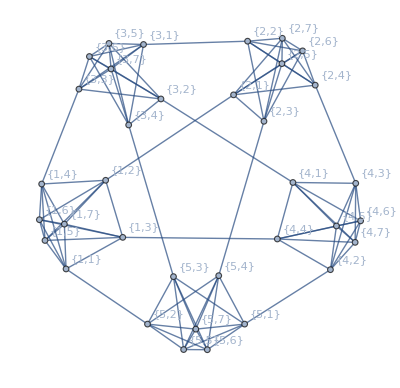

```mathematica
G[3,6,VertexLabels->Automatic]
```

```mathematica
Spectrum[%]
```

{{Root-2.61Root[-1+22 #1-7 #1^2-18 #1^3-2 #1^4+#1^5&,1]-2.6100317386539094,4},{Root-1.74Root[-1+22 #1-7 #1^2-18 #1^3-2 #1^4+#1^5&,2]-1.73763233450845,4},{-1,14},{Root0.0462Root[-1+22 #1-7 #1^2-18 #1^3-2 #1^4+#1^5&,3]0.04621530258780768,4},{Root0.880Root[-1+22 #1-7 #1^2-18 #1^3-2 #1^4+#1^5&,4]0.8800302144433776,4},{Root5.42Root[-1+22 #1-7 #1^2-18 #1^3-2 #1^4+#1^5&,5]5.421418556131174,4},{6,1}}

```mathematica
H[sigma_,k_,opts___]:=Graph[Join[
Flatten[Table[{i,u}<->{i,v},{i,2sigma-1},{u,2sigma-1,k},{v,u+1,k+1}],2],
Flatten[Table[{{i,u}<->{i,v},{i,u+1}<->{i,v}},{i,2sigma-1},{u,1,2sigma-3,2},{v,u+2,k+1}],3],
Flatten[Table[{i,2j}<->{Mod[i+1,2sigma-1,1],2j-1},{i,2sigma-1},{j,sigma-1}],1]
],opts]
```

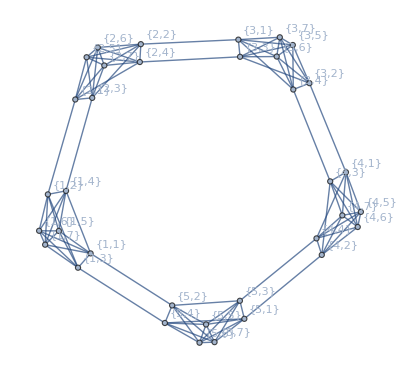

```mathematica
H[3,6,VertexLabels->Automatic]
```

```mathematica
Spectrum[%20]//N
```

{{-2.90211,2.},{-2.17557,2.},{-1.96226,2.},{-1.65132,2.},{-1.,14.},{-0.0501476,2.},{0.175571,2.},{0.843469,2.},{0.902113,2.},{5.11879,2.},{5.70147,2.},{6.,1.}}

```mathematica
ClearAll[H]
```

```mathematica
H[sigma_,k_,opts___]:=Graph[Join[
Flatten[Table[{i,u}<->{i,v},{i,2sigma-1},{u,2sigma-1,k},{v,u+1,k+1}],2],
Flatten[Table[{{i,u}<->{i,v},{i,u+1}<->{i,v}},{i,2sigma-1},{u,1,2sigma-3,2},{v,u+2,k+1}],3],
TwoWayRule@@@Partition[Permute[Flatten[Table[{i,j},{i,2sigma-1},{j,2sigma-2}],1],RandomPermutation[(2sigma-1)(2sigma-2)]],2]
],opts]
```

```mathematica
SecondEigenvalue[G[3,6]]
```

Root5.42Root[-1+22 #1-7 #1^2-18 #1^3-2 #1^4+#1^5&,5]5.421418556131174

```mathematica
{GraphPlot[#,VertexLabels->Automatic],SecondEigenvalue[#]}&/@MinimalBy[Select[Table[H[3,6],{i,100000}],ConnectedGraphQ],SecondEigenvalue]
```

$Aborted

More Testing

```mathematica
CirculantMatrix[b_]:=With[{n=Length[b],m=Length@First[b]},ArrayReshape[Riffle@@@NestList[RotateRight,b,n-1],{n*m,n*m}]]
```

```mathematica
b[m_,i_]/;i≤m-1:=SparseArray[{2i,2i-1}->1,{2m-2,2m-2}];
b[m_,i_]/;i≥m:=SparseArray[{4m-2i-3,4m-2i-2}->1,{2m-2,2m-2}]
```

```mathematica
J[n_]:=ConstantArray[1,{n,n}];
J[n_,2]:=SparseArray[{Band[{1,1}],Band[{2,1},Automatic,2],Band[{1,2},Automatic,2]}->1,{2n,2n}]
```

```mathematica
ClearAll[H,dH]
```

```mathematica
H[m_,k_,z_]:=-(x+1)/(k-2m+2-x)J[2m-2]-J[m-1,2]-x*IdentityMatrix[2m-2]+SparseArray[{Band[{2,1},Automatic,2]->z^Range[m-1],Band[{1,2},Automatic,2]->z^Range[2m-2,m,-1]},{2m-2,2m-2}]
```

```mathematica
dH[m_,j_]:=With[{g=GCD[2m-1,j]},(1+(g-1)/(k-2m+2-x)+(g(x+1))/(k-2m+2-x)Sum[(2x+Exp[(2 g i π I)/(2 m-1)]+Exp[(-2 g i π I)/(2 m-1)])/(x^2+2x-1+Exp[(2 g i π I)/(2 m-1)]+Exp[(-2 g i π I)/(2 m-1)]),{i,((2m-1)/g-1)/2}])(2ChebyshevT[(2m-1)/g,(x+1)/2])^g/(x+1)]
```

```mathematica
H[5,k,Exp[2Pi*I*3/9]]//Det//FullSimplify//Factor
```

((1+x)^2 (-2+2 x+x^2)^2 (9-2 k-7 x+2 k x-2 x^2+k x^2-x^3))/(-8+k-x)

```mathematica
dH[5,3]//FullSimplify//Factor
```

((1+x)^2 (-2+2 x+x^2)^2 (9-2 k-7 x+2 k x-2 x^2+k x^2-x^3))/(-8+k-x)

```mathematica
Table[{(k-2*5+2-x)dH[5,j]},{j,9}]//FullSimplify//Factor
```

{{9-2 k+11 x+2 k x-119 x^2+25 k x^2+38 x^3-16 k x^3+133 x^4-38 k x^4+11 x^5+2 k x^5-47 x^6+19 k x^6-28 x^7+8 k x^7-8 x^8+k x^8-x^9},{9-2 k+11 x+2 k x-119 x^2+25 k x^2+38 x^3-16 k x^3+133 x^4-38 k x^4+11 x^5+2 k x^5-47 x^6+19 k x^6-28 x^7+8 k x^7-8 x^8+k x^8-x^9},{-(1+x)^2 (-2+2 x+x^2)^2 (-9+2 k+7 x-2 k x+2 x^2-k x^2+x^3)},{9-2 k+11 x+2 k x-119 x^2+25 k x^2+38 x^3-16 k x^3+133 x^4-38 k x^4+11 x^5+2 k x^5-47 x^6+19 k x^6-28 x^7+8 k x^7-8 x^8+k x^8-x^9},{9-2 k+11 x+2 k x-119 x^2+25 k x^2+38 x^3-16 k x^3+133 x^4-38 k x^4+11 x^5+2 k x^5-47 x^6+19 k x^6-28 x^7+8 k x^7-8 x^8+k x^8-x^9},{-(1+x)^2 (-2+2 x+x^2)^2 (-9+2 k+7 x-2 k x+2 x^2-k x^2+x^3)},{9-2 k+11 x+2 k x-119 x^2+25 k x^2+38 x^3-16 k x^3+133 x^4-38 k x^4+11 x^5+2 k x^5-47 x^6+19 k x^6-28 x^7+8 k x^7-8 x^8+k x^8-x^9},{9-2 k+11 x+2 k x-119 x^2+25 k x^2+38 x^3-16 k x^3+133 x^4-38 k x^4+11 x^5+2 k x^5-47 x^6+19 k x^6-28 x^7+8 k x^7-8 x^8+k x^8-x^9},{(k-x) (1+x)^8}}

```mathematica
Table[{(k-2*8+2-x)dH[8,j]},{j,{1,3,5,15}}]//FullSimplify//Factor
```

{{15-2 k+47 x+2 k x-572 x^2+73 k x^2-103 x^3-48 k x^3+2853 x^4-402 k x^4+57 x^5+102 k x^5-4662 x^6+793 k x^6-1273 x^7+152 k x^7+3118 x^8-647 k x^8+1997 x^9-398 k x^9-292 x^10+101 k x^10-731 x^11+184 k x^11-349 x^12+76 k x^12-91 x^13+14 k x^13-14 x^14+k x^14-x^15},{-(1+x)^2 (1-6 x+x^2+4 x^3+x^4)^2 (15-k-44 x+6 k x+9 x^2-k x^2+16 x^3-4 k x^3+4 x^4-k x^4+x^5)},{-(1+x)^4 (-2+2 x+x^2)^4 (-15+2 k+13 x-2 k x+2 x^2-k x^2+x^3)},{(k-x) (1+x)^14}}

```mathematica
Table[{(k-2*11+2-x)dH[11,j]},{j,Divisors[2*11-1]}]//FullSimplify//Factor
```

{{21-2 k+107 x+2 k x-1577 x^2+145 k x^2-1216 x^3-96 k x^3+17190 x^4-1668 k x^4+5154 x^5+492 k x^5-66894 x^6+7250 k x^6-23588 x^7+688 k x^7+121301 x^8-15052 k x^8+71605 x^9-7334 k x^9-103273 x^10+14705 k x^10-102296 x^11+13960 k x^11+20396 x^12-3586 k x^12+61798 x^13-9896 k x^13+23420 x^14-3772 k x^14-6896 x^15+1392 k x^15-9645 x^16+1821 k x^16-4278 x^17+762 k x^17-1119 x^18+169 k x^18-190 x^19+20 k x^19-20 x^20+k x^20-x^21},{-(1+x)^2 (1+6 x-13 x^2-8 x^3+8 x^4+6 x^5+x^6)^2 (-k+85 x-6 k x-120 x^2+13 k x^2-55 x^3+8 k x^3+55 x^4-8 k x^4+29 x^5-6 k x^5+6 x^6-k x^6+x^7)},{-(1+x)^6 (-2+2 x+x^2)^6 (-21+2 k+19 x-2 k x+2 x^2-k x^2+x^3)},{(k-x) (1+x)^20}}

```mathematica
Table[Sum[GCD[2m-1,j]-1,{j,2m-1}],{m,2,11}]
```

{2,4,6,12,10,12,30,16,18,44}

```mathematica
Table[2m-2,{m,2,11}]
```

{2,4,6,8,10,12,14,16,18,20}

```mathematica
Table[With[{x=N@SecondEigenvalue[GMatrix[5,k]]},{9-2 k+(-7+2 k) x+(-2+k) x^2-x^3,9-2 k+(11+2 k) x+(-119+25 k) x^2+(38-16 k) x^3+(133-38 k) x^4+(11+2 k) x^5+(-47+19 k) x^6+(-28+8 k) x^7+(-8+k) x^8-x^9}],{k,10,20}]
```

{{-5.68434×10^-14,-7785.52},{5.68434×10^-14,-10695.9},{8.52651×10^-14,-14218.},{0.,-18405.9},{1.7053×10^-13,-23313.6},{1.13687×10^-13,-28995.1},{3.97904×10^-13,-35504.4},{4.54747×10^-13,-42895.5},{1.7053×10^-13,-51222.5},{3.41061×10^-13,-60539.3},{2.27374×10^-13,-70900.1}}

```mathematica
Table[{Max[x/.Solve[3-2 k+(-1+2 k) x+(-2+k) x^2-x^3==0,x]]>Max[x/.Solve[9-2 k+(-7+2 k) x+(-2+k) x^2-x^3==0,x]]},{k,10,100}]
```

{{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True}}

```mathematica
Reduce[(2m-1)(2(k+1)-3)+(2m-1)(m-1)≥2(2m-1)(k+1)-3&&m≥2]
```

k∈ℝ&&m≥7/2

```mathematica
(2m-1)(2(k+1)-3)+(2m-1)(m-1)-2(2m-1)(k+1)+3//FullSimplify
```

(-1+m) (-7+2 m)

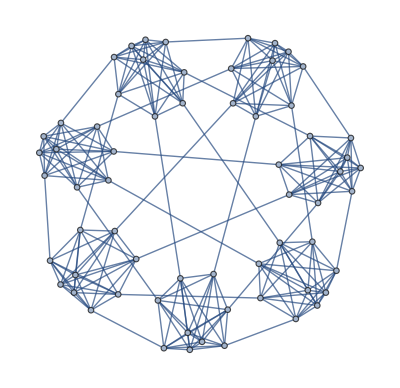

```mathematica
G[4,8]
```

```mathematica
ClearAll[s,p]
```

```mathematica
s[m_,zeta_]:=-Sum[(2x+zeta^i+zeta^-i)/(x^2+2x-1+zeta^i+zeta^-i),{i,m-1}](* ΣA^-1 *)
p[m_,zeta_]:=Product[x^2+2x-1+zeta^i+zeta^-i,{i,m-1}](* determinant of A *)
```

```mathematica
s[5,Exp[(2Pi*I*3)/9]]//FullSimplify//Factor
```

-(-7+7 x+8 x^2)/((1+x) (-2+2 x+x^2))

```mathematica
3*s[2,Exp[(2Pi*I*3)/9]]-2/(x+1)//FullSimplify//Factor
```

-(-7+7 x+8 x^2)/((1+x) (-2+2 x+x^2))

```mathematica
p[5,Exp[(2Pi*I*3)/9]]//FullSimplify//Factor
```

(1+x)^2 (-2+2 x+x^2)^3

```mathematica
p[2,Exp[(2Pi*I*3)/9]]^3(x+1)^2//FullSimplify//Factor
```

(1+x)^2 (-2+2 x+x^2)^3

Find ζ such that f_ζ contains the second largest eigenvalue.

```mathematica
ClearAll[t];t[m_]:=t[m]=Last@Last@NumericalSort@Table[{Max[x/.Solve[Factor[f[m,j]/.k->2m]==0,x]],j},{j,Most@Divisors[2m-1]}]
```

```mathematica
TableForm[Table[{m,t[m]==Last@Most@Divisors[2m-1]},{m,2,100}],TableDepth->2]
```

2 | True
3 | True
4 | True
5 | True
6 | True
7 | True
8 | True
9 | True
10 | True
11 | True
12 | True
13 | True
14 | True
15 | True
16 | True
17 | True
18 | True
19 | True
20 | True
21 | True
22 | True
23 | True
24 | True
25 | True
26 | True
27 | True
28 | True
29 | True
30 | True
31 | True
32 | True
33 | True
34 | True
35 | True
36 | True
37 | True
38 | True
39 | True
40 | True
41 | True
42 | True
43 | True
44 | True
45 | True
46 | True
47 | True
48 | True
49 | True
50 | True
51 | True
52 | True
53 | True
54 | True
55 | True
56 | True
57 | True
58 | True
59 | True
60 | True
61 | True
62 | True
63 | True
64 | True
65 | True
66 | True
67 | True
68 | True
69 | True
70 | True
71 | True
72 | True
73 | True
74 | True
75 | True
76 | True
77 | True
78 | True
79 | True
80 | True
81 | True
82 | True
83 | True
84 | True
85 | True
86 | True
87 | True
88 | True
89 | True
90 | True
91 | True
92 | True
93 | True
94 | True
95 | True
96 | True
97 | True
98 | True
99 | True
100 | True

```mathematica
ClearAll[t];
t[m_]:=NumberLinePlot@Table[x/.Solve[Factor[f[m,j]/.k->2m]==0,x],{j,Most@Divisors[2m-1]}]
```

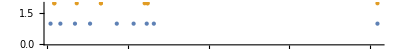

```mathematica
t[5]
```

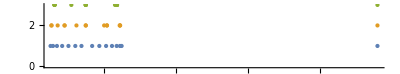

```mathematica
t[8]
```

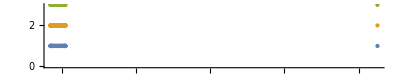

```mathematica
t[43]
```

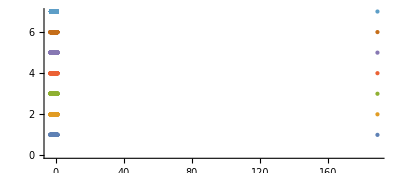

```mathematica
t[95]
```

```mathematica
2(x-k)ChebyshevT[3,(x+1)/2]/((x+1)/2)+3f[2,1]//Factor
```

9-2 k-7 x+2 k x-2 x^2+k x^2-x^3

```mathematica
(2m-1+g)/(2g)
```

```mathematica
Solve[(f[2,1]/.k->4)==0,x]
```

{{x→Root-2.20Root[5-7 #1-2 #1^2+#1^3&,1]-2.2044015503294316},{x→Root0.636Root[5-7 #1-2 #1^2+#1^3&,2]0.6355519407979245},{x→Root3.57Root[5-7 #1-2 #1^2+#1^3&,3]3.5688496095315068}}

```mathematica
f[2,1]//Factor
```

3-2 k-x+2 k x-2 x^2+k x^2-x^3

```mathematica
ChebyshevT[3,(x+1)/2]/((x+1)/2)//Factor
```

-2+2 x+x^2